```mathematica
NS["plinkinetti_graphs2"]
```

```mathematica
logt[x_,a_:1]=Sign[x]*Log[10,1+Abs[x/a]];
ilogt[x_,a_:1]=Sign[x]*(10^(Abs[x/a])-1);
logistic=LogisticSigmoid;
semilogistic[x_]=1-Exp[-x];
logit[x_]=Log[x/(1-x)];
xlogy[x_,y_]:=If[x>0,x*Log[x/y],0];
```

```mathematica
km[p1_,p2_]:=Total[Abs[Accumulate[p1-p2]]];
jsd[p1_,p2_]:=Total[MapThread[xlogy,{p1,(p1+p2)/2}]+MapThread[xlogy,{p2,(p1+p2)/2}]]/2;
```

```mathematica
face=Image[Import["face2.png"],ImageSize->20];
robot2=Image[Import["robot2.png"],ImageSize->20,ImageResolution->400];
```

```mathematica
wd="C:\\Users\\pglpm\\repositories\\plinkinetti\\comparisons11\\";
label="meankm2hga";
parts=Join[Range[1,15],Range[17,40]];
```

```mathematica
ClearAll[obs,pdists,rdists,params];obs=Import["observation_seqs.csv"];pdists[i_]:=pdists[i]=Import[wd<>"pdistr"<>ToString[i]<>"_"<>label<>".csv"];
rdists[i_]:=rdists[i]=Import[wd<>"rdistr"<>ToString[i]<>"_"<>label<>".csv"];
params=Import[wd<>"points_meankm2hga.csv"];
params=Insert[params,{16,Null,Null,Null,Null},16];
```

```mathematica
dist1=Import["rdistr_p1.csv"];
tpar=Import["params_p1.csv"];
```

```mathematica
<<"robotdistribution.m"
```

```mathematica
ClearAll[rdistsm];rdistsm[i_]:=rdistsm[i]=robotdistribution[pdists[i][[1]],params[[i,2;;]],obs[[i,2;;201]]];
```

```mathematica
adiffs=Table[Max@Abs@Flatten[(rdists[i]-rdistsm[i])],{i,parts}]
```

{5.1209×10^-15,9.02056×10^-16,1.24845×10^-13,5.55112×10^-16,9.57567×10^-15,2.30371×10^-15,4.74863×10^-14,1.35308×10^-15,2.77556×10^-16,5.13478×10^-16,3.83027×10^-15,2.28983×10^-15,0.000191377,1.249×10^-16,9.99201×10^-16,5.75928×10^-16,1.02349×10^-16,5.55112×10^-16,2.08639×10^-13,6.46705×10^-15,1.23512×10^-15,7.16094×10^-15,4.01068×10^-15,1.56847×10^-13,5.34295×10^-15,3.63598×10^-15,4.96825×10^-15,5.68989×10^-16,5.27356×10^-16,3.06422×10^-14,9.97119×10^-15,0.260346,7.49401×10^-16,6.7002×10^-14,3.88578×10^-15,8.04912×10^-16,1.14249×10^-10,1.09357×10^-14,8.57647×10^-15}

```mathematica
aratios=Table[Max@Abs@Flatten[1-rdists[i]/rdistsm[i]],{i,parts}]
```

{4.75175×10^-14,2.93099×10^-14,9.77107×10^-13,2.38313×10^-9,6.87117×10^-13,4.19664×10^-14,6.2685×10^-11,5.27356×10^-14,9.88098×10^-15,8.52576×10^-10,6.38045×10^-13,8.30447×10^-14,0.0311109,8.65974×10^-15,2.30882×10^-9,1.5099×10^-14,8.21565×10^-15,5.9952×10^-15,2.11631×10^-12,7.9714×10^-14,1.15463×10^-14,2.83107×10^-14,1.90292×10^-13,8.23785×10^-13,7.27196×10^-14,4.26326×10^-14,6.66134×10^-14,7.99361×10^-15,7.99361×10^-15,4.84945×10^-13,2.40252×10^-13,94.6863,9.32587×10^-15,2.9543×10^-13,2.55795×10^-13,7.77156×10^-15,2.05244×10^-7,6.92779×10^-14,3.25414×10^-9}

```mathematica
kdists=Table[{i,Max@Table[km[rdistsm[i][[j]],rdists[i][[j]]],{j,201}]},{i,parts}]
```

{{1,5.37343×10^-14},{2,5.4512×10^-14},{3,1.37335×10^-13},{4,2.74607×10^-14},{5,1.29089×10^-13},{6,1.15163×10^-13},{7,3.72928×10^-13},{8,7.22339×10^-14},{9,1.80509×10^-14},{10,2.75946×10^-14},{11,9.52767×10^-14},{12,3.62908×10^-14},{13,0.0108418},{14,1.85824×10^-14},{15,4.08195×10^-14},{17,3.8183×10^-14},{18,1.59742×10^-14},{19,4.72998×10^-14},{20,2.03841×10^-12},{21,6.78884×10^-14},{22,3.25912×10^-14},{23,5.28466×10^-14},{24,4.20015×10^-14},{25,1.90249×10^-12},{26,1.83252×10^-13},{27,4.53778×10^-14},{28,2.19371×10^-13},{29,4.05728×10^-14},{30,3.06469×10^-14},{31,1.14403×10^-12},{32,9.35987×10^-14},{33,6.63926},{34,4.23659×10^-14},{35,7.50136×10^-13},{36,1.03964×10^-13},{37,3.76851×10^-14},{38,1.07014×10^-9},{39,1.44676×10^-13},{40,7.76371×10^-14}}

```mathematica
kdists=Table[{i,Max@Table[jsd[rdistsm[i][[j]],rdists[i][[j]]],{j,201}]},{i,parts}]
```

{{1,6.05586×10^-17},{2,4.86181×10^-17},{3,1.11022×10^-16},{4,7.98827×10^-17},{5,9.95445×10^-17},{6,3.45142×10^-17},{7,7.47851×10^-17},{8,1.0679×10^-16},{9,3.33352×10^-17},{10,6.40422×10^-17},{11,5.87845×10^-17},{12,4.16723×10^-17},{13,4.47948×10^-6},{14,4.37364×10^-17},{15,7.70938×10^-17},{17,4.82085×10^-17},{18,3.82637×10^-17},{19,7.32687×10^-17},{20,6.26231×10^-17},{21,8.69526×10^-17},{22,6.41597×10^-17},{23,8.10672×10^-17},{24,7.96404×10^-17},{25,7.68965×10^-17},{26,3.6594×10^-17},{27,7.38278×10^-17},{28,7.21143×10^-17},{29,1.43531×10^-16},{30,6.08972×10^-17},{31,9.99833×10^-17},{32,7.07293×10^-17},{33,0.462471},{34,6.19714×10^-17},{35,1.05709×10^-16},{36,7.21128×10^-17},{37,7.67998×10^-17},{38,9.30943×10^-17},{39,8.18203×10^-17},{40,1.06988×10^-16}}

```mathematica
diffs=Table[Print[i];Max@Abs@Flatten[2*(rdists[i]-rdistsm[i])/(rdists[i]+rdistsm[i])],{i,parts}]
```

{4.74593×10^-14,2.9239×10^-14,9.772×10^-13,2.38313×10^-9,6.87196×10^-13,4.19428×10^-14,6.26851×10^-11,5.28037×10^-14,9.87212×10^-15,8.52576×10^-10,6.3807×10^-13,8.31322×10^-14,0.0316025,8.76218×10^-15,2.30882×10^-9,1.5049×10^-14,8.12083×10^-15,6.01508×10^-15,2.11639×10^-12,7.98518×10^-14,1.15834×10^-14,2.83378×10^-14,1.90345×10^-13,8.23889×10^-13,7.27092×10^-14,4.25266×10^-14,6.66617×10^-14,7.90418×10^-15,7.91474×10^-15,4.85012×10^-13,2.40178×10^-13,1.99687,9.23892×10^-15,2.95425×10^-13,2.55769×10^-13,7.68349×10^-15,2.05244×10^-7,6.93293×10^-14,3.25414×10^-9}

```mathematica
i=33;n=Length[obs[[i,2;;201]]];
cumf=Table[0,{n+1},{40}];
Do[cumf[[j+1,obs[[i,j+1]]]]=1,{j,n}];
cumf=Accumulate[cumf];
```

```mathematica
cumfr=T@Import["cumul13.csv"];
```

```mathematica
Dimensions[cumf]
```

{201,40}

```mathematica
cumf==cumfr
```

False

```mathematica
tempb=T@Import["bcoef.csv"];
```

```mathematica
m=105;pf=pdists[33][[1]];stub=10;tempbm=Table[(stub*pf+cumf[[m]]-cumf[[m-u]])/(stub+u),{u,0,m-1}];
```

```mathematica
tempb[[1;;4]]//MF
```

(3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 0.0107362 | 0.0122699 | 0.0138037 | 0.0230061 | 0.0276074 | 0.0276074 | 0.0276074 | 0.0276074 | 0.053681 | 0.0598159 | 0.0782209 | 0.0674847 | 0.0521472 | 0.0260736 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 0.0322086 | 0.0644172 | 0.0874233 | 0.0782209 | 0.0674847 | 0.0567485 | 0.0199387 | 0.0199387 | 0.0199387 | 0.0199387 | 0.0168712 | 0.00920246 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9
3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9 | 0.00976018 | 0.0111545 | 0.0125488 | 0.0209147 | 0.0250976 | 0.0250976 | 0.0250976 | 0.0250976 | 0.0488009 | 0.0543781 | 0.0711099 | 0.0613497 | 0.0474066 | 0.0237033 | 3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9 | 0.0909091 | 3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9 | 0.0292805 | 0.0585611 | 0.0794757 | 0.0711099 | 0.0613497 | 0.0515895 | 0.018126 | 0.018126 | 0.018126 | 0.018126 | 0.0153374 | 0.00836587 | 3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9
2.79642×10^-9 | 2.79642×10^-9 | 2.79642×10^-9 | 0.00894683 | 0.010225 | 0.0115031 | 0.0191718 | 0.0230061 | 0.0230061 | 0.0230061 | 0.0230061 | 0.0447341 | 0.0498466 | 0.065184 | 0.0562372 | 0.043456 | 0.021728 | 2.79642×10^-9 | 2.79642×10^-9 | 2.79642×10^-9 | 0.0833333 | 0.0833333 | 2.79642×10^-9 | 2.79642×10^-9 | 2.79642×10^-9 | 0.0268405 | 0.053681 | 0.0728528 | 0.065184 | 0.0562372 | 0.0472904 | 0.0166155 | 0.0166155 | 0.0166155 | 0.0166155 | 0.0140593 | 0.00766871 | 2.79642×10^-9 | 2.79642×10^-9 | 2.79642×10^-9
2.58131×10^-9 | 2.58131×10^-9 | 2.58131×10^-9 | 0.00825861 | 0.00943842 | 0.0106182 | 0.017697 | 0.0212364 | 0.0212364 | 0.0212364 | 0.0212364 | 0.0412931 | 0.0460123 | 0.0601699 | 0.0519113 | 0.0401133 | 0.0200566 | 2.58131×10^-9 | 0.0769231 | 2.58131×10^-9 | 0.0769231 | 0.0769231 | 2.58131×10^-9 | 2.58131×10^-9 | 2.58131×10^-9 | 0.0247758 | 0.0495517 | 0.0672487 | 0.0601699 | 0.0519113 | 0.0436527 | 0.0153374 | 0.0153374 | 0.0153374 | 0.0153374 | 0.0129778 | 0.00707881 | 2.58131×10^-9 | 2.58131×10^-9 | 2.58131×10^-9)

```mathematica
tempbm[[1;;4]]//MF
```

(3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 0.0107362 | 0.0122699 | 0.0138037 | 0.0230061 | 0.0276074 | 0.0276074 | 0.0276074 | 0.0276074 | 0.053681 | 0.0598159 | 0.0782209 | 0.0674847 | 0.0521472 | 0.0260736 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9 | 0.0322086 | 0.0644172 | 0.0874233 | 0.0782209 | 0.0674847 | 0.0567485 | 0.0199387 | 0.0199387 | 0.0199387 | 0.0199387 | 0.0168712 | 0.00920246 | 3.3557×10^-9 | 3.3557×10^-9 | 3.3557×10^-9
3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9 | 0.00976018 | 0.0111545 | 0.0125488 | 0.0209147 | 0.0250976 | 0.0250976 | 0.0250976 | 0.0250976 | 0.0488009 | 0.0543781 | 0.0711099 | 0.0613497 | 0.0474066 | 0.0237033 | 3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9 | 0.0909091 | 3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9 | 0.0292805 | 0.0585611 | 0.0794757 | 0.0711099 | 0.0613497 | 0.0515895 | 0.018126 | 0.018126 | 0.018126 | 0.018126 | 0.0153374 | 0.00836587 | 3.05064×10^-9 | 3.05064×10^-9 | 3.05064×10^-9
2.79642×10^-9 | 2.79642×10^-9 | 2.79642×10^-9 | 0.00894683 | 0.010225 | 0.0115031 | 0.0191718 | 0.0230061 | 0.0230061 | 0.0230061 | 0.0230061 | 0.0447341 | 0.0498466 | 0.065184 | 0.0562372 | 0.043456 | 0.021728 | 2.79642×10^-9 | 2.79642×10^-9 | 2.79642×10^-9 | 0.0833333 | 0.0833333 | 2.79642×10^-9 | 2.79642×10^-9 | 2.79642×10^-9 | 0.0268405 | 0.053681 | 0.0728528 | 0.065184 | 0.0562372 | 0.0472904 | 0.0166155 | 0.0166155 | 0.0166155 | 0.0166155 | 0.0140593 | 0.00766871 | 2.79642×10^-9 | 2.79642×10^-9 | 2.79642×10^-9
2.58131×10^-9 | 2.58131×10^-9 | 2.58131×10^-9 | 0.00825861 | 0.00943842 | 0.0106182 | 0.017697 | 0.0212364 | 0.0212364 | 0.0212364 | 0.0212364 | 0.0412931 | 0.0460123 | 0.0601699 | 0.0519113 | 0.0401133 | 0.0200566 | 2.58131×10^-9 | 0.0769231 | 2.58131×10^-9 | 0.0769231 | 0.0769231 | 2.58131×10^-9 | 2.58131×10^-9 | 2.58131×10^-9 | 0.0247758 | 0.0495517 | 0.0672487 | 0.0601699 | 0.0519113 | 0.0436527 | 0.0153374 | 0.0153374 | 0.0153374 | 0.0153374 | 0.0129778 | 0.00707881 | 2.58131×10^-9 | 2.58131×10^-9 | 2.58131×10^-9)

```mathematica
tempbm==tempb
```

True

```mathematica
params[[33]]
```

{33,0.59379,-1073.91,177.099,295.151}

```mathematica
rtest=Import["rtest.csv"];
```

```mathematica
rtest==rdistsm[33]
```

True

```mathematica
mean[distr_]:=distr.Range[1,40];
std[distr_]:=Sqrt[(distr.(Range[1,40]^2))-(mean[distr]^2)];
```

```mathematica
Dimensions[std@rdists[1]]
```

{201}

```mathematica
myfontsize=15;
```

```mathematica
i=1;ListPlot[{T[{Range[1,200],obs[[i,2;;]]}],T[{Range[0,200],mean@rdists[i]}],T[{Range[0,200],mean@dist1}]},Joined->{True,True,True,True},PlotMarkers->{{Graphics[{Disk[{0,0},0.01]}],0.02},"","",""},PlotRange->{1,40},PlotStyle->{{grey,Thin},{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]},{green,Thick,DotDashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","mean"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"outcome",face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}]
```

-Graphics-

```mathematica
ListPlot[{T[{Range[0,200],std@rdists[i]}],T[{Range[0,200],std@dist1}]},Joined->{True,True,True},PlotRange->{0,15},PlotStyle->{{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","std"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}]
```

-Graphics-

```mathematica
(* Plot means *)
```

```mathematica
myfontsize=15;Do[plot=ListPlot[{T[{Range[1,200],obs[[i,2;;]]}],T[{Range[0,200],mean@pdists[i]}],T[{Range[0,200],mean@rdistsm[i]}]},Joined->{True,True,True},PlotMarkers->{{Graphics[{Disk[{0,0},0.01]}],0.02},"",""},PlotRange->{1,40},PlotStyle->{{grey,Thin},{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","mean"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"outcome",face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0["graph_km\\means_p"<>ToString[i]<>"_km",plot],
{i,parts}]
```

```mathematica
maxstd=Max@Flatten@Table[{std@pdists[i],std@rdistsm[i]},{i,parts}];
minstd=Min@Flatten@Table[{std@pdists[i],std@rdistsm[i]},{i,parts}];
```

```mathematica
(* Plot stds *)
```

```mathematica
Do[plot=ListPlot[{T[{Range[0,200],std@pdists[i]}],T[{Range[0,200],std@rdistsm[i]}]},Joined->{True,True,True},PlotRange->{minstd,maxstd},PlotStyle->{{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","std"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0["graph_km\\std_p"<>ToString[i]<>"_km",plot],
{i,parts}]
```

```mathematica
ClearAll[jst,kmt];jst[i_]:=Table[jsd[pdists[i][[j]],rdistsm[i][[j]]],{j,201}];
kmt[i_]:=Table[km[pdists[i][[j]],rdistsm[i][[j]]],{j,201}];
```

```mathematica
maxjst=Max@Flatten@Table[jst[i],{i,parts}];maxkmt=Max@Flatten@Table[kmt[i],{i,parts}];
```

```mathematica
(* Plot discrepancies *)
```

```mathematica
imgpad={{45,50},{45,10}};Do[plot1=ListPlot[T[{Range[0,200],kmt[i]}],Joined->True,PlotRange->{0,maxkmt},PlotStyle->{green,Thick,Opacity[0.75]},Axes->None,Frame->{True,True,False,False},FrameStyle->{Directive[Black,myfontsize,Thickness[1/500],FontFamily->Auto],Directive[green,myfontsize,Thickness[1/500],FontFamily->Auto],Auto,Auto},
FrameTicks->All,
FrameLabel->{Style["observation",Black,myfontsize,Thickness[1/50],FontFamily->Auto],Style["K distance",green,myfontsize,Thickness[1/50],FontFamily->Auto]},
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"K distance"},{0.25,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/1.7},ImagePadding->imgpad];

plot2=ListPlot[T[{Range[0,200],jst[i]}],Joined->True,PlotRange->{0,maxjst},PlotStyle->{yellow,Thick,Dashed,Opacity[0.75]},Axes->None,Frame->{False,False,False,True},
FrameTicks->All,FrameStyle->{Auto,Auto,Auto,Directive[yellow,myfontsize,Thickness[1/500],FontFamily->Auto]},
FrameLabel->{{None,Style["JS distance",yellow,myfontsize,Thickness[1/50],FontFamily->Auto]},{None,None}},
PlotLabel->mystyle[""],
PlotLegends->mylegends[{"JS distance"},{0.75,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/1.7},ImagePadding->imgpad];

expdf0["graph_km\\discr_p"<>ToString[i]<>"_km",Overlay[{plot1,plot2}]]
,{i,parts}]
```

```mathematica
cpl[s_,m_,p_]:=p[[1]]+p[[2]]*m+p[[3]]*s;cp[s_,m_,p_]:=LogisticSigmoid[cpl[s,m,p]];
```

```mathematica
cpi[i_]:=cpi[i]=Table[{m,s,cp[s,m,params[[i,3;;5]]]},{s,0,m-1},{m,1,199}]
```

```mathematica
(* Plot changepoint function *)
```

```mathematica
DensityPlot[cp[s,m,tpar[[1,2;;]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},{0,1}},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->red,Frame->{{False,True},{True,False}},ColorFunction->(GrayLevel[1-#]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,FrameTicks->All,
PlotLabel->mystyle["changepoint function participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[[i,2]]],Scaled[{0.1,0.9}],{-1,0}]]
```

-Graphics-

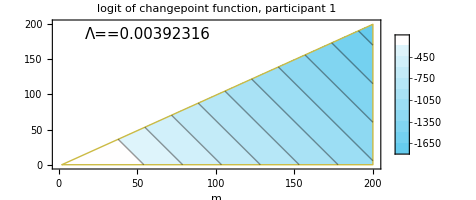

```mathematica
minh=Minimize[{cpl[s,m,tpar[[1,2;;]]],2≤m≤200,1≤s≤ m-1},{s,m}][[1]];
maxh=Maximize[{cpl[s,m,tpar[[1,2;;]]],2≤m≤200,1≤s≤ m-1},{s,m}][[1]];

suph=Max@Abs@{maxh,minh};

plot=ContourPlot[cpl[s,m,tpar[[1,2;;]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},All},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->yellow,Frame->{{False,True},{True,False}},ColorFunction->(mycolorfunction[#,suph]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,Contours->10,FrameTicks->All,
PlotLabel->mystyle["logit of changepoint function, participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[[i,2]]],Scaled[{0.1,0.9}],{-1,0}]]
```

```mathematica
Do[minh=Minimize[{cpl[s,m,tpar[[1,2;;]]],2≤m≤200,1≤s≤ m-1},{s,m}][[1]];
maxh=Maximize[{cpl[s,m,tpar[[1,2;;]]],2≤m≤200,1≤s≤ m-1},{s,m}][[1]];

suph=Max@Abs@{maxh,minh};

plot=ContourPlot[cpl[s,m,tpar[[1,2;;]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},All},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->yellow,Frame->{{False,True},{True,False}},ColorFunction->(mycolorfunction[#,suph]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,Contours->10,FrameTicks->All,
PlotLabel->mystyle["logit of changepoint function, participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[[i,2]]],Scaled[{0.1,0.9}],{-1,0}]];
expng["graph_km\\logitchangep_p"<>ToString[i]<>"_km",plot]
,{i,parts}]
```

```mathematica
Do[plot=DensityPlot[cp[s-1,m-1,params[[i,3;;5]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},{0,1}},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->red,Frame->{{False,True},{True,False}},ColorFunction->(GrayLevel[1-#]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,FrameTicks->All,
PlotLabel->mystyle["changepoint function participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[[i,2]]],Scaled[{0.1,0.9}],{-1,0}]];
expng["graph_km\\changep_p"<>ToString[i]<>"_km",plot]
,{i,parts}]
```

```mathematica
allcpfs=Table[DensityPlot[cp[s-1,m-1,params[[i,3;;5]]],{m,2,200},{s,1,199},PlotRange->{{0,201},{-1,201},{0,1}},RegionFunction->Function[{x,y},2≤x≤200&&1≤y≤x-1],BoundaryStyle->red,Frame->{{False,True},{True,False}},ColorFunction->(GrayLevel[1-#]&),ColorFunctionScaling->False,PlotRangeClipping->False,PlotPoints->100,FrameTicks->All,
PlotLabel->mystyle["participant "<>ToString[i]],PlotLegends->Placed[All,Left],AspectRatio->1/2,FrameLabel->{{None,Style[v,Black,myfontsize,Thickness[1/50],FontFamily->Auto]},{Style[m,Black,myfontsize,Thickness[1/50],FontFamily->Auto],None}},Epilog->Text[mystyle[Style[Λ,Italic] ==Exp@ params[[i,2]]],Scaled[{0.1,0.9}],{-1,0}]],{i,parts}];
```

```mathematica
Export["allcpfs.pdf",Grid[ArrayReshape[allcpfs,{8,5}],Spacings->{0,0}]];
```

```mathematica
expng["testme"]
```

testme.png

```mathematica
n=L
```

```mathematica
n=Length[obs[[6]]]-1;
cumf=Table[0,{n},{40}];
Do[cumf[[i,obs[[6,i+1]]]]=1,{i,n}];
cumf=Accumulate[cumf];
```

```mathematica
Do[plot=ListPlot[{T[{Range[1,200],obs[[1,2;;]]}],T[{Range[0,200],mean@pdists[i]}],T[{Range[0,200],mean@rdists[i]}]},Joined->{True,True,True},PlotMarkers->{{Graphics[{Disk[{0,0},0.01]}],0.02},"",""},PlotRange->{1,40},PlotStyle->{{grey,Thin},{red,Thick,Opacity[0.75]},{purpleblue,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","mean"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{"outcome",face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0["means_p"<>ToString[i]<>"_km",plot],
{i,parts}]
```

```mathematica
expdf0["testrl"]
```

testrl.pdf

```mathematica
Do[jst=Table[jsd[pdists[i][[j]],rdists[i][[j]]],{j,201}];
kmt=Table[km[pdists[i][[j]],rdists[i][[j]]],{j,201}];

plot=ListPlot[{T[{Range[0,200],kmt}],T[{Range[0,200],jst}]},Joined->{True,True,True},PlotRange->{minstd,maxstd},PlotStyle->{{green,Thick,Opacity[0.75]},{yellow,Thick,Dashed,Opacity[0.75]}},Axes->None,Frame->{True,True,False,False},Evaluate@myframestyle[15],
FrameLabel->myaxes[{"observation","std"}],
PlotLabel->mystyle["participant "<>ToString[i]],
PlotLegends->mylegends[{face,robot2},{0.5,1}],AspectRatio->1/2,ImageSize->{a4shortside,a4shortside/2}];

expdf0["std_p"<>ToString[i]<>"_km",plot],
{i,parts}]
```

```mathematica
jsds=Table[
Mean@Table[jsd[pdists[i][[j]],rdists[i][[j]]],{j,201}]
,{i,parts}]
```

{0.0993772,0.00364069,0.148928,0.0569079,0.261384,0.0390831,0.251955,0.0905575,0.0416622,0.134381,0.0389707,0.0493197,0.0921684,0.00683605,0.270714,0.00534013,0.00371694,0.0682766,0.0852479,0.0587686,0.0782703,0.0650108,0.0445418,0.048148,0.0139286,0.0630536,0.0718753,0.0557745,0.0732668,0.1051,0.0744426,0.294216,0.0575291,0.121505,0.161204,0.071989,0.141243,0.121521,0.230279}

```mathematica
Through[{Mean,Std,Quantile[#,1/4]&,Quantile[#,3/4]&,Max}[jsds]]
```

{0.0948753,0.0750031,0.048148,0.121521,0.294216}

```mathematica
kms=Table[
Mean[Table[km[pdists[i][[j]],rdists[i][[j]]],{j,201}]^2]
,{i,parts}]
```

{2.61276,0.0894319,9.63938,1.36529,5.85108,3.39938,12.2772,2.12124,2.33435,1.99767,1.92105,1.88026,5.08389,0.582363,7.40793,0.46411,0.343312,2.34322,7.65474,1.1845,2.65684,1.54865,0.920667,0.583014,0.730777,1.91472,3.63718,0.684,8.82315,10.6941,2.91042,18.9769,0.69848,2.75067,2.41051,1.4302,2.66746,3.11275,4.8803}

```mathematica
Through[{Mean,Std,Quantile[#,1/4]&,Quantile[#,3/4]&,Max}[kms]]
```

{3.656,3.89207,1.1845,4.8803,18.9769}

```mathematica
wd="C:\\Users\\pglpm\\repositories\\plinkinetti\\comparisons7c\\";
label="mean1jsd";
parts=Join[Range[1,15],Range[17,40]];
```

```mathematica
Do[pdists[i]=Import[wd<>"pdistr"<>ToString[i]<>"_"<>label<>".csv"];
rdists[i]=Import[wd<>"rdistr"<>ToString[i]<>"_"<>label<>".csv"];
,{i,parts}]
```

```mathematica
jsds=Table[
Mean@Table[jsd[pdists[i][[j]],rdists[i][[j]]],{j,201}]
,{i,parts}]
```

{0.0765796,0.00355378,0.135515,0.0552162,0.14369,0.034513,0.183412,0.0183988,0.0392441,0.105663,0.0308545,0.0451551,0.0904422,0.00533001,0.173889,0.00478623,0.00364021,0.0546038,0.0624696,0.0640398,0.0788823,0.0648099,0.0337751,0.0479645,0.00849954,0.0624737,0.0596919,0.0520734,0.0399005,0.10093,0.0734605,0.0732725,0.0573807,0.0997069,0.134951,0.0719141,0.132379,0.121005,0.207985}

```mathematica
Through[{Mean,Std,Quantile[#,1/4]&,Quantile[#,3/4]&,Max}[jsds]]
```

{0.0731295,0.0502303,0.0392441,0.10093,0.207985}

```mathematica
kms=Table[
Mean[Table[km[pdists[i][[j]],rdists[i][[j]]],{j,201}]^2]
,{i,parts}]
```

{5.06443,0.126556,14.2716,2.13163,11.7793,4.64877,17.3631,4.83972,3.09642,4.72131,2.83446,1.78999,5.37131,0.70554,10.9121,0.747784,0.589372,5.51525,11.9982,1.44782,2.87916,1.58501,0.697489,1.6505,1.62409,2.55814,3.88064,0.86981,17.7739,11.6176,3.61975,2.44471,0.706656,3.26717,3.28327,1.43893,3.08307,3.82769,11.6331}

```mathematica
Through[{Mean,Std,Quantile[#,1/4]&,Quantile[#,3/4]&,Max}[kms]]
```

{4.83065,4.72439,1.58501,5.37131,17.7739}